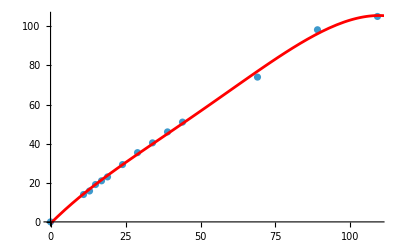

-0.7938274173018051 + 1.5294566788791966*(abs_dist) - 0.0167715067642669*(abs_dist)**2 + 0.00024722073358174275*(abs_dist)**3 - 1.284671288987042e-6*(abs_dist)**4

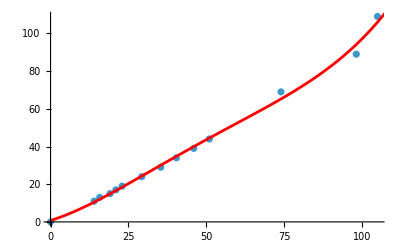

0.727104914847282 + 0.5147081989789882*(ball_dist) + 0.016366529704736815*(ball_dist)**2 - 0.00026196059702118856*(ball_dist)**3 + 1.4312212575440405e-6*(ball_dist)**4

```mathematica
(*Input format is {dist to edge of bot, pixel distance}*)
data={{-9,0},{2,14},{4,15.8},{6,19.1},{8,21.0},{10,23.0},{15,29.3},{20,35.4},{25,40.4},{30,46.0},{35,51.0},{60,74.0},{80,98.2},{100,105}};
data[[All,1]]+=9; 
n=4; (*what order polynomial to fit*)
bestFit=Fit[data,Table[x^k,{k,0,n}],x];
Show[ListPlot[data,PlotRange->All],Plot[{bestFit},{x,0,120},PlotStyle->Red]]
pythonStr=ToString[bestFit/.{x->abs_dist},InputForm];
pythonStr=StringReplace[pythonStr,"*^"->"e"];
pythonStr=StringReplace[pythonStr,"^"->"**"];
pythonStr
data=Reverse/@data;

n=4;
bestFit=Fit[data,Table[x^k,{k,0,n}],x];
Show[ListPlot[data,PlotRange->All],Plot[{bestFit},{x,0,120},PlotStyle->Red]]
pythonStr=ToString[bestFit/.{x->ball_dist},InputForm];
pythonStr=StringReplace[pythonStr,"*^"->"e"];
pythonStr=StringReplace[pythonStr,"^"->"**"];
pythonStr
```